# Packed Arrays

## An efficient internal storage format in Mathematica 4 Mathematica 4 开始的一种高效内部存储格式

Rob Knapp
Numerical Algorithms Development
Wolfram Research, Inc.
rknapp@wolfram.com

原文链接：http://library.wolfram.com/infocenter/Demos/391/
翻译：妈妈说睡觉前不许吃苹果_20160313
注：部分代码由于原文mma版本过低无法运行，已修改以适应新版本，本文代码在Mathematica 10.4.0中测试通过。
注：文中蓝色字体为翻译，紫色字体为苹果自行添加语句或内容，不确保观点正确
注：本文并未介绍Packed Array的底层架构/原理/实现，但是讨论了如何使用及注意事项等内容。

20160313：初稿
20160830：增加一部分代码提速示范

While packed arrays may sound quite mysterious and deep, the idea is really quite simple. When it is clearly appropriate to represent a list of a single type machine numbers (integer, real, or complex) internally as an array, Mathematica does so. The basic technology is actually there in Mathematica 3.0, and is visible in the List operations that were added to the compiler. Basically what has been done for Mathematica 4 is to extend this representation to kernel functions where it is appropriate. The internal representation is essentially invisible to you as a user (you have to use functions in the Developer` context to even see it) so you do not have to worry about it. However, understanding the packed array representation can help you write faster, more ncode.
Packed arrays可能有点神秘，但是它的思想是十分简单的。当我们想用数组(Array)清楚恰当的表示一个单类型机器数(Integer/Real/Complex)列表(List)时，Mathematica则可以用一种高效的方式去表示这个列表。这种方式的基本想法在Mathematica 3.0中就有了，例如编译器中的List操作(应该是说Compiler这个函数的Listable属性？待定)。在Mathematica 4.0中这种思路被拓展到合适的内置函数中，当内置函数适合用Packed Arrays时，它就会自动使用，当然这个操作是对使用者是不可见的过程，如果使用者想主动操作相关内容，可以使用Developer函数包。理解Packed Array的思路有利于写出高效、节约内存的代码。

## Representations of data in Mathematica

If you enter a list in Mathematica,
当我们在Mathematica中输入一个列表：

```mathematica
list = {1,2,3,4}
```

{1,2,3,4}

its internal representation may be different from the OutputForm. The basic common representation for lists (and all expressions) is given by the FullForm.
它的内部表达式可能和它的输出形式(OutputForm)是不同的，我们可以用FullForm查看这个表达式的内部表现形式：

```mathematica
FullForm[list]
```

List[1,2,3,4]

Each integer you see in the list is itself an expression. Internally in the Mathematica C code, the data stored carries information about the type of expression (in this case, list, or number which is a machine integer).
在这个列表中，你看到的每个整数，其内部表达式都是它自身。在Mathematica底层C代码中，数据存储包含数据的表达式类型，例如上例中包含List及机器整数这两个类型(按照我的理解因此上例中实际存储了4个信息分别表示这个数据是机器整数类型)。

If you enter the data a different way,
如果我们换个方式输入数据：

```mathematica
packed = Range[4]
```

{1,2,3,4}

it is internally stored in a different way. The basic print forms are all the same. For all intents and purposes it is the same.
这个数据的内部存储方式就会变得不同，虽然两种输入方式的输出形式是完全一样的，而且我们的使用目的也是一样的。

```mathematica
packed === list
```

True

You can only tell that it is stored in a different way by using a Developer` context function:
使用Developer可以知道这两者使用了不同的存储方式：

```mathematica
Developer`PackedArrayQ /@ {list, packed}
```

{False,True}

## Advantages of packed arrays

There are two advantages of packed arrays, memory and speed. 
Packed Arrays有两个优点，内存和速度。

The memory is the most obvious of these.
很明显内存节约了：

```mathematica
ByteCount[a=N[Range[1000]]]
```

8304

If you change the first element to be a different type, the result cannot be stored as a packed array.
a中所有的元素都是浮点数，如果我们将第一个元素改成整型数，那么它将无法被存储成Packed Array，其内存占用将会增多：

```mathematica
ByteCount[b=a;b⟦1⟧=1;b]
N[%/(%%)]
```

24200

2.91426

The speed advantage typically comes in common operations.
效率优势在一些通用操作中也很明显：

```mathematica
Timing[Do[a+a,{1000}]]
Timing[Do[b+b,{1000}]]
```

{0.004936,Null}

{0.471254,Null}

Understanding why the timing difference occurs is the key to knowing when packed arrays will help your code run faster.
理解上述两个代码时间差的产生原因，有助于理解什么时候packed arrays能够使得代码效率提高。

In the first operation, a is stored as a packed array, so when Plus sees it, it knows all of the elements are machine real numbers, so that internally, a function which adds arrays of real numbers is used. Except for overflow and underflow checking, which Mathematica does, this is done as fast as you could get by writing a loop to do the addition in a C-program for two arrays of machine numbers.
在第一个运算中，a是被存储成packed array，所以Plus知道a中所有的元素都是机器实数(Real)，因此在内部使用了机器实数数列相加的一种算法，这种算法，除了溢出(overflow)和下溢出(underflow)，其他的和使用C编写的2个机器实数相加的代码一样快(在某些情况下，使用mma进行数值计算，可以写出基本和C语言一样快的代码，但对使用者要求较高，因此mma并不太适合大型数值计算)。

In the second operation, b is stored as List[…], so what happens first is Plus is threaded over the lists, producing (roughly) the following.
在第二个操作中，b被存储成List[...]，所以Plus首先逐项作用到整个列表中，如下所示

```mathematica
{b[[1]]+b[[1]],b[[2]]+b[[2]],....}
```

Plus processes 1000 expressions. For each pair of numbers, Plus uses the information attached to those numbers (i.e., real, integer, machine, bignum, and so forth) to determine what function to use to do the actual adding. This all takes time and accounts for nearly all of the difference here.
Plus产生了1000个表达式。对每一组数，Plus都需要根据输入数的类型(Real/Integer/machine/bignum等)，来使用不同的算法进行计算。这些都需要花费时间，造成了上述两个操作的时间差。

There are different ways that packed arrays can speed things up, but this exemplifies the type which typically gives the greatest increase in speed.
Packed Array有很多提高代码效率的方式，上述方式是其中一种比较典型的方式。

## When do you get packed arrays?

When trying to write efficient programs, this is a very important question. There are three important situations that commonly produce packed arrays.
什么时候我们会得到Packed Arrays？当我们试图写出一个高效的代码时，这就是一个很重要的问题了。有三种产生Packed Arrays的方法。

#### 1. Listable and structural operations with packed array input (where the output can be a packed array.) 当输入数据是Packed Array时，Listable属性和结构操作将会输出Packed Array。

Listable operations mean those with the attribute Listable. 
Listable操作即函数的Listable属性。

```mathematica
Select[Names["System`*"], MemberQ[Attributes[#], Listable]&]//Short
```

{Abs,AbsArg,AiryAi,«273»,WhittakerM,WhittakerW,Zeta}

The majority of which will produce packed arrays given packed array arguments.
在传入Packed Array参数时，上述函数大多数将产生Packed Array输出。

Structural operations mean commands like Part, Join, Transpose, and so forth, which act on the structure of an expression.
结构操作即Part/Join/Transpose等，是对表达式结构进行操作。

即使输入参数不是Packed Array，有些函数也会尝试自动对结果Packed Array，这种方式归于哪一类情况并不明确，因为不清楚Sin函数的内部实现。当然，这需要输入参数的长度大于250，这和后文说的内容有关。

```mathematica
data = Developer`FromPackedArray@RandomComplex[1+I,260];

Developer`PackedArrayQ[data]
Developer`PackedArrayQ[Sin[data]]

data2 = Developer`FromPackedArray@RandomComplex[1+I,240];

Developer`PackedArrayQ[data2]
Developer`PackedArrayQ[Sin[data2]]
```

False

True

False

False

#### 2. Functions that use an internal array format for machine numbers. 使用机器数作为内部数组格式的函数。

Fourier is a good example of this:
例如Fourier：

```mathematica
Developer`PackedArrayQ[{1.,2.,3.,4.}]
Developer`PackedArrayQ[Fourier[{1.,2.,3.,4.}]]
```

False

True

Whether the input is a packed array or not, if Fourier does its computation with machine numbers, it internally uses arrays already, so it is natural to give the output in terms of a packed array.
不论输入参数是否是Packed Array，Fourier如果使用机器数进行计算，那么它的返回自然使用Packed Array。

#### 3. Functions which can quickly determine from simple input that the output could be a packed array. 那些可以快速根据简单的输入判断是否能够产生Packed Array输出的函数。

You have already used one example in this class, Range. In Range[4], it is easy to see before generating any numbers that the result can be represented as a packed array.
上文早已使用了这类产生Packed Array输出的情况，Range。Range[4]很明显应该产生一个Packed Array结果。

For something like the following, it is a little more difficult to determine.
当然有时候，这类判断并不是很显而易见：

```mathematica
Timing[Developer`PackedArrayQ[data = Table[RandomReal[],{100000},{2}]]]
```

{0.039369,True}

Commands like this are handled by auto-compilation. However, since trying the compiler does take some time, there is a (user modifiable) threshold length that must be exceeded before compilation is attempted.
上述代码使用了自动编译。当然由于采用自动编译是需要时间的，因此需要一个阈值长度(用户可修改)，当列表长度超过阈值长度时才会尝试使用自动编译。

(以下内容来自SE的讨论)
此阈值长度可以查看，并且是可以用户修改的。下面以Table的Auto-Compilation为例讨论。

```mathematica
SystemOptions["CompileOptions"->"TableCompileLength"]
```

{CompileOptions→{TableCompileLength→250}}

Table的Auto-Compilation(或者说Auto-Packed)的阈值长度是250，因此有以下现象产生：

```mathematica
Developer`PackedArrayQ[Table[RandomReal[],#]]&/@{248,249,250,251}
```

{False,False,True,True}

当然并不是说Table的长度超过250且结果可以是Packed时Table就一定会Auto-Compilation，Table是否会Auto-Compilation不仅与长度相关，也与计算的内容相关，例如下面的例子。当然我们也是可以手动对下面的例子进行Packed操作，以方便方便后续的计算。

```mathematica
Developer`PackedArrayQ[
data=Table[i/.x_/;x>300:>RandomReal[],{i,1,251}]
]
Developer`PackedArrayQ[
data=Developer`ToPackedArray[data]
]
```

False

True

Table的Auto-Compilation的阈值长度是250，超过此长度才会尝试Auto-Compilation，既然可以手动修改，是不是阈值长度应该调成0呢？不是，因为尝试进行Auto-Compilation也是需要时间的，下面例子可以说明这一点。当列表长度较小时(下面两个例子中的临界点分别是30和160左右)，uncompiled的代码运行速度比compiled的代码快。

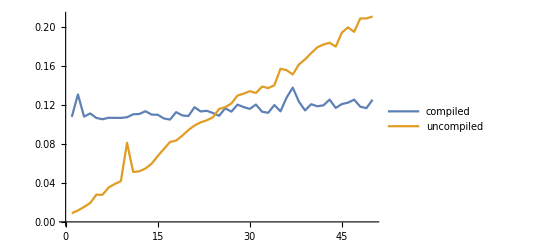

```mathematica
someCalculation=First@Timing@Do[
With[{y=RandomReal[]},Table[Abs[i-y]/(1+ⅇ^Sin[i y] i^2-0.5(i+y)^23),{i,#}]],
{1000}
]&;

SetSystemOptions["CompileOptions"->{"TableCompileLength"->∞}];
uncompiled=Map[someCalculation,Range[1,50]];

SetSystemOptions["CompileOptions"->{"TableCompileLength"->1}];
compiled=Map[someCalculation,Range[1,50]];

ListLinePlot[{compiled,uncompiled},PlotLegends->{"compiled","uncompiled"}]
```

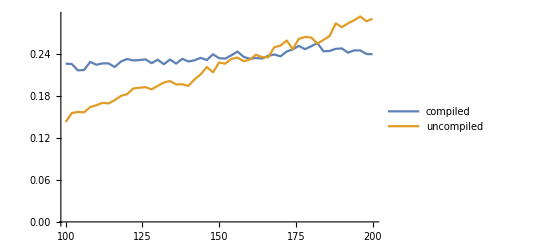

```mathematica
SetSystemOptions["CompileOptions"->{"TableCompileLength"->∞}];
some=First@Timing@Do[
With[{y=RandomReal[]},Table[i+y,{i,#}]],
{5000}
]&;
uncompiled=Map[{#,some@#}&,Range[100,200,2]];

SetSystemOptions["CompileOptions"->{"TableCompileLength"->1}];
compiled=Map[{#,some@#}&,Range[100,200,2]];

ListLinePlot[{compiled,uncompiled},PlotLegends->{"compiled","uncompiled"}]
```

## Can packed arrays ever be slower?

Yes. Here is an example.
Packed Array可能会造成代码效率变低吗？是的，下面就是一个例子。

```mathematica
data=Table[RandomReal[],{100000},{2}];
f[{a_,b_}] := a^2-b^2;

Timing[Developer`PackedArrayQ[Map[f,data]]]
Timing[Developer`PackedArrayQ[udata = Developer`FromPackedArray[data]]]
Timing[Developer`PackedArrayQ[Map[f,udata]]]
```

{0.252405,False}

{0.010595,False}

{0.194725,False}

However, if you inline the function, the auto-compilation can work.
然而，如果将f函数内嵌，那么自动编译(Auto-Compilation)将会起作用，此时运行效率很高。

```mathematica
Timing[Developer`PackedArrayQ[Map[#⟦1⟧^2 + #⟦2⟧^2&, data]]]
```

{0.021451,True}

It is not always the case that things are so easily patched up. Some commands are incompatible with packed arrays. However, before complaining too loudly about these cases, please take into account the whole time going into your computation. In the above example, you were not taking into account the time it took to generate the random list. Without auto-compilation and packed arrays, it takes quite a bit longer to compute.
有时候事情并没有看起来的那么简单。有些函数与Packed Araays并不兼容。关于这一点无法解释更多。但是我们也需要注意到一点，如果没有Auto-Compilation，那么产生data的时间会增多，尽管后面因为Auto-Compilation反而增加的运算时间，在本例中两者造成的影响相互抵消掉以后显然Auto-Compilation还是功大于过的，也就是运行效率更高。
当然，这个例子中产生一个随机数组使用的是Table+RandomReal组合，因为本文写的时候是没有RandomReal这个函数的，现在更加应该用RandomReal函数，因为其效率很高。通常情况下mma自己编写函数没有内置函数快，因此尽量使用mma内置函数，特别是每个函数都有很多用法，不求全会，但求全知道，写的时候能想起来大概有那么一个用法然后去查。

```mathematica
SetSystemOptions["CompileOptions"->{"TableCompileLength"->∞}];
Timing[Developer`PackedArrayQ[data=Table[RandomReal[],{100000},{2}]]]

SetSystemOptions["CompileOptions"->{"TableCompileLength"->250}];
Timing[Developer`PackedArrayQ[data=Table[RandomReal[],{100000},{2}]]]

Timing[Developer`PackedArrayQ[data=RandomReal[{0,1},{100000,2}]]]
```

{0.082543,False}

{0.025178,True}

{0.001593,True}

(以下内容来自苹果自己的探索)
上面这个例子，还有个有点意思的地方。上面用的是Map来内嵌纯函数，由于有两个参数，所以需要写成#⟦1⟧和#⟦2⟧，有时候为了代码更好看(我个人不太喜欢这么多括号，个人习惯)，所以会用Apply，即#1^2+#2^2&@@@data。首先将Map和Apply的Auto-Compilation阈值长度调为∞，可以看到Map比Apply慢，且两者的结果都不是Packed Array。

```mathematica
SetSystemOptions["CompileOptions"->{"MapCompileLength"->∞,"ApplyCompileLength"->∞}];

data=RandomReal[{0,1},{1000000,2}];
Timing[Developer`PackedArrayQ[(#⟦1⟧)^2+ (#⟦2⟧)^2&/@ data]]
Timing[Developer`PackedArrayQ[#1^2+#2^2&@@@data]]
```

{2.8508,False}

{1.56729,False}

其次将Map和Apply的Auto-Compilation阈值长度调为0。可以看到Map的运行效率比之前快很多。然而Apply的运行效率并没有发生变化，且输出结果仍然不是Packed Array。因此在选择使用Map还是Apply的时候请慎重考虑。

```mathematica
SetSystemOptions["CompileOptions"->{"MapCompileLength"->0,"ApplyCompileLength"->0}];

data=RandomReal[{0,1},{1000000,2}];
Timing[Developer`PackedArrayQ[(#⟦1⟧)^2+ (#⟦2⟧)^2&/@ data]]
Timing[Developer`PackedArrayQ[#1^2+#2^2&@@@data]]
```

{0.218327,True}

{1.57078,False}

按照上面的例子，ApplyCompileLength岂不是完全没有意义所以Mathematica将其默认值设置为Infinity了？不，这篇SE帖子里写道：“ Setting the value of ...CompileLength to Infinity is effectively disabling the auto-compilation. You can see that “ApplyCompileLength” has this value. This is because it can only compile 3 heads: Times, Plus, and List”。所以ApplyCompileLength还是有价值的，但是考虑到之前说的Auto-Compilation本身也是需要花费时间的，所以请自行判断ApplyCompileLength设置成多少合适。

```mathematica
data=RandomReal[{0,1},{1000000,2}];

SetSystemOptions["CompileOptions"->{"ApplyCompileLength"->0}];
Timing[Developer`PackedArrayQ[Plus@@@data]]
Timing[Developer`PackedArrayQ[Times@@@data]]

SetSystemOptions["CompileOptions"->{"ApplyCompileLength"->Infinity}];
Timing[Developer`PackedArrayQ[Plus@@@data]]
Timing[Developer`PackedArrayQ[Times@@@data]]
```

{0.178112,True}

{0.175603,True}

{0.49285,False}

{0.508077,False}

(以下内容来自SE讨论)
前文有一句“这种算法，除了溢出(overflow)和下溢出(underflow)，其他的和使用C编写的2个机器实数数组相加的代码一样快”。Mathematica会进行溢出(overflow)和下溢出(underflow)检测。以下这个例子可以说明如果检测到下溢出，会使得Auto-Compiled失效。
首先看下面这个例子，可以看到运算效率很低。由于Fold过程中会产生Underflow，所以先关闭(因为mma的$MinNumber比$MinMachineNumber小很多很多)。虽然此代码中Fold的运行长度(10^6)比阈值长度(100)大，但是结果仍然不是Packed Array。

```mathematica
{$MinMachineNumber,$MinNumber}

SystemOptions["CompileOptions"->"FoldCompileLength"]

SetSystemOptions["CatchMachineUnderflow"->False];
Timing@With[{x=Sin[10.5]},Fold[{(#⟦1⟧x)/(#2+1),#⟦2⟧+Tan[#⟦1⟧]}&,{x,1.0},N@Range[10^6]]]

Developer`PackedArrayQ@Last@%
```

{2.22507×10^-308,6.22968824967532196119819746965503015872`15.954589770191005*^-1355718576299610}

{CompileOptions→{FoldCompileLength→100}}

{4.16786,{0.,0.105747}}

False

其原因是当Fold运行到165时，检测到了underflow，此时Auto-Compila失效了。

```mathematica
Timing@With[{x=Sin[10.5]},Fold[{(#⟦1⟧x)/(#2+1),#⟦2⟧+Tan[#⟦1⟧]}&,{x,1.0},N@Range[165]]]
Developer`PackedArrayQ@Last@%

Timing@With[{x=Sin[10.5]},Fold[{(#⟦1⟧x)/(#2+1),#⟦2⟧+Tan[#⟦1⟧]}&,{x,1.0},N@Range[166]]]
Developer`PackedArrayQ@Last@%
```

{0.000314,{6.37932×10^-308,0.105747}}

True

{0.001072,{-3.36039×10^-310,0.105747}}

False

解决方法也是有的，套上Compile，并且关闭溢出检查(请确保没有overflow，否则会出现问题，例如参考RuntimeOptions帮助文档中的例子)。

```mathematica
cf=With[{x=Sin[10.5]},Compile[{{arg,_Real,1}},Fold[{(#⟦1⟧x)/(#2+1),#⟦2⟧+Tan[#⟦1⟧]}&,{x,1.0},N@Range[166]],"RuntimeOptions"->"Speed"]];
Timing[cf[N[Range[10^6]]]]
Developer`PackedArrayQ@Last@%
```

{0.008315,{-3.36039×10^-310,0.105747}}

True

这里提到了一个比较严重的问题
有时候我们试图给我们的自定义函数一个Listable的属性来提高运行效率(因为惯例是利用内置函数的Listable属性比利用Map要快很多)，但是自定义函数的Listable仅仅是对输入列表参数进行逐项作用，并没有Auto-Compilation作用，例如下面的例子，还不如Map快，当然这里x^2仅仅是个例子，最快的方法肯定是利用Power的Listable属性。

```mathematica
data=RandomReal[1,1000000];
Timing[Developer`PackedArrayQ[Function[x,x^2,Listable]@data]]
Timing[Developer`PackedArrayQ[Function[x,x^2]/@data]]
Timing[Developer`PackedArrayQ[data^2]]
```

{1.16524,False}

{0.051531,True}

{0.030309,True}

## How do I write code that takes advantage of packed arrays?

The most important thing to do is to make sure that you do operations on lists of elements all at once or in groups whenever possible.
怎么在写代码的时候运用出Packed Arrays的优点呢？在写代码时请确保你是在对数组进行list或group操作。

The good news is that this programming principle has not really changed from Mathematica 1.0. Efficient code in Mathematica has always used functional and list based constructs.
Mathematica的编程原则从Mathematica 1.0开始就没有变过，高效的mma代码总是基于函数式或list-based结构。(所以本文虽然写于Mathematica 4.0时代，但是仍然适用于Mathematica 10.4.0；同时UnitStep/Abs/Sign等这类Listable的函数的运行效率特别特别高，请经常性使用这类函数。)

The one other thing to keep in mind is that type needs to be consistent for there to even be a packed array representation.
需要注意的是Packed Arrays内的数据类型(Real/Integer/Complex等)是需要一致的。

Some aids are provided that can help you in putting together your code.
下面是一个小帮助，当Packed Arrays变成Unpacked Arrays时会给出提示。

```mathematica
Developer`PackedArrayForm[Range[1000]]
SetSystemOptions["PackedArrayOptions"->{"UnpackMessage"->True}]

Timing[Apply[Plus, N[Range[1000]]]]
Developer`PackedArrayQ@Last@%

Timing[Tr[N[Range[1000]]]]

SetSystemOptions["PackedArrayOptions"->{"UnpackMessage"->False}];
```

PackedArray[Integer,<1000>]

PackedArrayOptions→{ListableAutoPackLength→250,PackedArrayMathLinkRead→True,UnpackMessage→True}

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {1000}.

{0.130788,500500.}

False

{0.000222,500500.}

Sometimes, you know your code will run more efficiently if you pack the input beforehand. 
有时候手动将数据packed将会提高代码效率(原文中的例子由于旧函数在新版本中的改进，已无法体现出代码效率变化，故换了个例子，此例子为我曾经写的代码的片段)。

```mathematica
n=270;dx=1.4;dn=6;
state0=RandomChoice[{0.001,0.999}->{1,0},{n,n}];
state=Developer`ToPackedArray[state0];
Row[{"state0 packed?: ",Developer`PackedArrayQ@state0}]
Row[{"state packed?: ",Developer`PackedArrayQ@state}]

pMat=Developer`ToPackedArray[0.1Exp[-dx^2Array[Norm[{##}-dn-1]^2&,{2dn+1,2dn+1}]]
];
CalcProbability[state_]:=(1-Sign[state])ListConvolve[pMat,1-Unitize[state-1],{{dn+1,dn+1}},0];

Timing@Developer`PackedArrayQ@CalcProbability[state0]
Timing@Developer`PackedArrayQ@CalcProbability[state]
```

state0 packed?: False

state packed?: True

{0.04345,True}

{0.013257,True}

## Example: LU Decomposition

Here is the code for actually doing an LU decomposition (factorization) from the package LinearAlgebra`GaussianElimination. Since this functionality exists in the kernel, the real purpose of this package is pedagogical, but the original author seems to have gone too far with the intent to stick to standard C-looking code so that people familiar only with procedural code can understand it. The result is a prime example of how you should not write code in Mathematica. Let’s see why and how you can improve it.
下面是一个LU分解的代码，由于LU分解已经是内置函数了(LUDecomposition)，所以下面的代码是个很好的例子，可以示范在Mathematica中应该怎么写代码，如何提高运行效率。当然这个例子仅仅说明了一个提升代码效率的方法，但是却很重要，即基于List进行操作。

```mathematica
lufactor[aa_]:=Module[{a=aa,pivot,ii,iip,i,ip,j,k,mpiv,m,n=Length[aa],tmp},
pivot=Table[i,{i,n}];
For[ii=1,ii≤n,ii++,(*for each row do...*)
(*find a pivot*)
mpiv=Abs[a⟦pivot⟦ii⟧,ii⟧];
k=ii;
For[i=ii+1,i≤n,i++,
tmp=Abs[a⟦pivot⟦i⟧,ii⟧];
If[tmp>mpiv,mpiv=tmp; k=i]
];
tmp=pivot⟦ii⟧;
pivot⟦ii⟧=iip=pivot⟦k⟧;
pivot⟦k⟧=tmp;
mpiv=a⟦iip,ii⟧;
(*calculate and store the multipliers and reduce the other elements.*)
For[i=ii+1,i≤n,i++,
ip=pivot⟦i⟧;
m=a⟦ip,ii⟧=a⟦ip,ii⟧/mpiv;
For[j=ii+1,j≤n,j++,
a⟦ip,j⟧-=m*a⟦iip,j⟧
];
];
];
LU[a,pivot]
]
```

Here are two test examples so you can compare timings of different versions.
下面是2个不同情况的测试数据

```mathematica
SeedRandom[1234];
machine = RandomReal[{0,1},{80,80}];
big =RandomReal[{0,1},{40,40},WorkingPrecision->20];

Timing[luf = lufactor[machine];]
Timing[LUDecomposition[machine];]
Timing[lufb = lufactor[big];]
Timing[LUDecomposition[big];]
```

{0.884522,Null}

{0.00776,Null}

{0.185521,Null}

{0.035471,Null}

Ouch! You are a factor of 300 slower in the machine case and a factor of 5 slower in the bignum example. Before screaming an exasperated “Mathematica is just too slow,” lets try to improve the code.
显然，自定义函数很慢，接下来我们将提升运行效率。

The first thing noticed is that this code is using For to handle the loops.  In Mathematica, For is slower than the alternative iterator constructs. Try to avoid using For in innermost loops unless it would make for more complicated code. In this example simply changing from For to Do makes a substantial difference.
首先是用Do替代For循环。在Mathematica中For循环是个比较慢的迭代器，Do更快一些(理由可以参考这个帖子，不过说实话过分追求Do替代For倒也不至于，除非是For的判断条件运行需要很长很长时间，否则For和Do的运行效率差异不是很大，不足以影响我更喜欢For的这种排版方式，即将循环次数等内容放在前面)。除非是需要写一些比较复杂的代码，否则请用Do替代For。

```mathematica
lufactor1[aa_]:=Module[{a=aa,pivot,ii,iip,i,ip,j,k,mpiv,m,n=Length[aa],tmp},
pivot=Table[i,{i,n}];
Do[(*for each row do...*)
(*find a pivot*)
mpiv=Abs[a⟦pivot⟦ii⟧,ii⟧];
k=ii;
Do[
tmp=Abs[a⟦pivot⟦i⟧,ii⟧];
If[tmp>mpiv,mpiv=tmp; k=i],
{i,ii+1,n}
];
tmp=pivot⟦ii⟧;
pivot⟦ii⟧=iip=pivot⟦k⟧;
pivot⟦k⟧=tmp;
mpiv=a⟦iip,ii⟧;
(*calculate and store the multipliers and reduce the other.*)
Do[
ip=pivot⟦i⟧;
m=a⟦ip,ii⟧=a⟦ip,ii⟧/mpiv;
Do[a⟦ip,j⟧-=m*a⟦iip,j⟧,{j,ii+1,n}],
{i,ii+1,n}
],
{ii,n}];
LU[a,pivot]
]
```

```mathematica
Timing[lufactor1[machine] === luf]
Timing[lufactor1[big] === lufb]
```

{0.523716,True}

{0.069722,True}

The next change will help make the code more readable. At this point, it won’t seem to make much of a speed difference, but it does help. The idea is to replace the lines of code finding the correct pivot to use with a function.
第二步，我们将增强代码的可读性。增强可读性并不会造成比较大的代码运行效率差别，但是是很有用的。这里的想法是将寻找correct pivot的代码写成自定义函数。(写Mathematica代码请勤写自定义函数，并起个有意义的函数名，并写上合适的注释，善待自己善待他人，免得半年后作者自己都看不懂自己的代码)

```mathematica
SetAttributes[FindPivot, HoldFirst];
FindPivot[pivots_, a_, c_] := 
Module[{k=First[MaxPosition[Abs[a⟦Take[pivots,{c,-1}],c⟧]]]+c-1},pivots⟦{c,k}⟧=pivots⟦{k,c}⟧;pivots⟦c⟧
];
```

This function finds which of the possible pivots (in column c, rows c and above) is largest in absolute value, and swaps with the one in row c.
涉及LU分解算法，没看懂，但是大意就是寻找pivot，并交换什么什么行。

This, in turn, uses the simple function, and puts it into the main function.
定义一个简单的函数，并且放到主函数中：

```mathematica
MaxPosition[x_] := First[Position[x, Max[x]]];
lufactor2[aa_]:=Module[{a=aa,pivot,ii,iip,i,ip,j,k,mpiv,m,n=Length[aa],tmp},
pivot=Table[i,{i,n}];
Do[(*for each row do...*)
iip=FindPivot[pivot,a,ii];
mpiv=a⟦iip,ii⟧;
(*calculate and store the multipliers and reduce the other.*)
Do[
ip=pivot⟦i⟧;
m=a⟦ip,ii⟧=a⟦ip,ii⟧/mpiv;
Do[a⟦ip,j⟧-=m*a⟦iip,j⟧,{j,ii+1,n}],
{i,ii+1,n}
],
{ii,n}];
LU[a,pivot]
]

Timing[lufactor2[machine] === luf]
Timing[lufactor2[big] === lufb]
```

{0.540022,True}

{0.074371,True}

You are still going in the right direction, but there is no big savings. The place to look for big savings is the innermost loop. The next change replaces the innermost loop by giving Mathematica commands that operate on all the elements of a list:
现在我们正走在正确编写Mathematica程序的道路上，不过到现在为止程序效率的改进还很小。程序内的循环还有很大改进空间，使用。接下来使用Mathematica提供的Part批量赋值语句取代原来的Do循环来提高效率。

```mathematica
lufactor3[aa_]:=Module[{a=aa,pivot,ii,iip,i,ip,j,rc,mpiv,m,n=Length[aa]},
pivot=Table[i,{i,n}];
Do[(*for each row do...*)
iip = FindPivot[pivot, a,ii];
mpiv=a⟦iip,ii⟧;
(*calculate and store the multipliers and reduce the other.*)
rc = Table[j,{j,ii+1,n}];
Do[
ip=pivot⟦i⟧;
m=-(a⟦ip,ii⟧/=mpiv);
(*此处原语句为Do[a⟦ip,j⟧-=m*a⟦iip,j⟧,{j,ii+1,n}]*)
a⟦ip,rc⟧+=m a⟦iip,rc⟧,
{i,ii+1,n}
],
{ii,n}
];
LU[a,pivot]
]

Timing[lufactor3[machine] === luf]
luf3 = lufactor3[machine];
{Max[Abs[First[luf3] - First[luf]]],luf3⟦2⟧ === luf⟦2⟧}
(*仅仅存在一个很小的误差*)
```

{0.03416,False}

{2.57572×10^-14,True}

So replacing the innermost loop was spectacularly successful. There is still a set of nested loops that can be worked on though. 
可以看到运行效率有很大的提高。接下来继续替换掉一个循环，效率又有了很大的提高。

```mathematica
lufactor4[aa_]:=Module[{a=aa,pivot,ii,iip,i,ip,j,rc,prc,mpiv,m,n=Length[aa],row},
pivot=Table[i,{i,n}];
Do[(*for each row do...*)
iip = FindPivot[pivot, a,ii];
mpiv=a⟦iip,ii⟧;
(*calculate and store the multipliers and reduce the other.*)
rc=Table[j,{j,ii+1,n}];
prc=pivot⟦rc⟧;
m=-(a⟦prc,ii⟧/=mpiv);
row = a⟦iip,rc⟧;
a⟦prc,rc⟧+=Map[(row #)&, m],
{ii,n}
];
LU[a,pivot]
]

Timing[lufactor4[machine] === luf3]
Timing[lufactor4[big] === lufb]
```

{0.03271,True}

{0.049324,True}

以下是我研究生时写的一串代码，现在来看，可提速的空间很大。

```mathematica
Clear["Global`*"]
(*坐标空间——三维高斯分布*)
R=7(*fm*);n=1000000;
(*概率密度函数归一化系数*)
(*n组随机坐标(Pr,Pθ,Pφ),r满足一定分布，0≤θ≤π,-π≤φ≤π*)
(Rrθφ=Join[List/@RandomVariate[ProbabilityDistribution[r^2 E^(-r^2/(2 R^2)),{r,0,3R},Method->"Normalize"],n],{ArcCos[#1],# Pi}&@@@RandomReal[{-1,1},{n,2}],2])//Developer`PackedArrayQ//AbsoluteTiming
```

{4.2403,False}

RandomVariate的改动空间已经不大了。但θ和φ的产生过程，有很大的改动空间。

```mathematica
(*初始代码*)
{ArcCos[#1],#2 Pi}&@@@RandomReal[{-1,1},{n,2}]//Developer`PackedArrayQ//AbsoluteTiming
(*Apply改成Map，这样可以运用上文说的Auto-Compiled*)
{ArcCos[#⟦1⟧],#⟦2⟧Pi}&/@RandomReal[1,{n,2}]//Developer`PackedArrayQ//AbsoluteTiming
(*利用内置函数的Listable属性减少函数调用花销*)
Transpose[{ArcCos[2RandomReal[1,n]-1], RandomReal[{-π,π},n]}]//Developer`PackedArrayQ//AbsoluteTiming
(*@酱紫君 指出使用指定算法的随机会比不指定算法的随机更快一些。但目前对指定算法可能造成的其他影响还不清楚*)
BlockRandom[
SeedRandom[Method->"MKL"];
Transpose[{ArcCos[2RandomReal[1,n]-1], RandomReal[{-π,π},n]}]
]//Developer`PackedArrayQ//AbsoluteTiming
```

{1.75825,False}

{0.181636,True}

{0.040702,True}

{0.028232,True}

全文终。